```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = (w*bPred*P*C +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[M],bPredSub->bPredSub[M],(*σPred->σPred[M],kC->kCons[M],*)μPred->μPred[M](*,Sub->Sub[M]*)};
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+w*b*P)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],b->b[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC,0==eqnR},{P,C,R}]];
```

```mathematica
Psol = P/.LVSS[[5]]
Csol = C/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[M])/w-(8 μ[M])/w+((-3 √kRes √w √α √bPred[M] √Y[M]+√(9 kRes w α bPred[M] Y[M]-16 λ[M] (Sub (-1+w) bPredSub[M]+μPred[M]))) (kRes w α bPred[M] Y[M]+2 (Sub (-1+w) bPredSub[M]+μPred[M]) σ[M]))/(√kRes w^(3/2) √α √bPred[M] √Y[M] (Sub (-1+w) bPredSub[M]+μPred[M])))/(8 b[M])

(Sub (-1+w) bPredSub[M]+μPred[M])/(w bPred[M])

kRes/4+(√kRes √(9 kRes w α bPred[M] Y[M]-16 λ[M] (Sub (-1+w) bPredSub[M]+μPred[M])))/(4 √w √α √bPred[M] √Y[M])

```mathematica
CsolNoSubsidies= Csol/.w->1
```

μPred[M]/bPred[M]

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C],D[eqnP,R]},
{D[eqnC,P],D[eqnC,C],D[eqnC,R]},
{D[eqnR,P],D[eqnR,C],D[eqnR,R]}})/.{P->Psol,C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ppmr_fit_table_revreps.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
(*predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];*)
(*predatedconsumerdensity[Mp_,M_]:=1/Ypred[Mp,M];*)
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*1/Ypred[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];
b[M_] :=predmortalityfull[OptPredMass[M],M];

predgrowth =  FullSimplify[predgrowthrateperconsumer[Mp,M]]; (*predatedconsumerdensity without the 1/Yield*)
predgrowthfull[Mp_,M_]:=Evaluate[predgrowth//Simplify];
bPred[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPred[M_]:=λPred[OptPredMass[M]];*)
bPredSub[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPredSub[M_]:=Sub*λPred[OptPredMass[M]];*)



(*Predator starvation*)
σPred[M_]:=(1/τsig [OptPredMass[M]]);
kCons[M_]:=PreyDensityTheoreticalMax[M]; (*Consumer theroetical maximum*)
(*Predator mortality*)
μPred[M_] := (a0*(Exp[a1*a2*OptPredMass[M]^(b1+b2)]-1)*OptPredMass[M]^(b0-b1-b2))/(a1*a2);   (* this is the consumer death rate*)
(*Subsidies could be set as mass dependent or mass-independent*)
(*Sub[M_]:=CsolNoSubsidies;*)
Sub=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];(*1*)(*0.1*CsolNoSubsidies;*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Sub=1*Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]]
```

10.4527

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

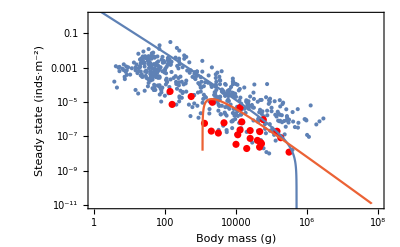

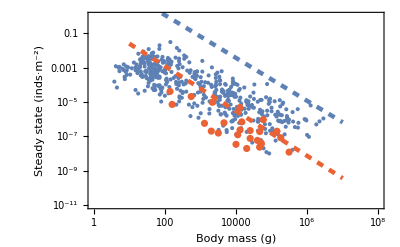

```mathematica
PercentGrowthConsumer=0.995;
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.w->PercentGrowthConsumer,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/M)*Psol/.w->PercentGrowthConsumer,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.w->PercentGrowthConsumer,{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.w->PercentGrowthConsumer,{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

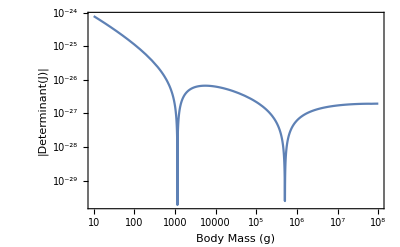

```mathematica
LogLogPlot[ Abs[Det[(JacobianFullModel/.{w->PercentGrowthConsumer})]],{M,10^1,10^8},Frame->True,FrameLabel->{"Body Mass (g)","|Determinant(J)|"}]
```